# Calculate h_ab^R1 in the Lorenz gauge

```mathematica
r0=6.05;
```

## Load the data and define orbital parameters

```mathematica
(*SetDirectory[NotebookDirectory[]<>"h1_ab data/hlmi/"];*)
SetDirectory["~/Code/SecondOrder/FirstOrderData/data/ret_data/"];
```

```mathematica
r0ToString[r_Integer]:=ToString[r]
r0ToString[r_]:=ToString[N[r]]
```

```mathematica
Clear[drh]
```

```mathematica
M=1;
pm=+1;
file="hlmi_r"<>r0ToString[r0]<>"_high_acc.dat";
data=Sort[Import[file],#1[[3]]<#2[[3]]||(#1[[3]]==#2[[3]]&&#1[[1]]<#2[[1]])||(#1[[3]]==#2[[3]]&&#1[[1]]==#2[[1]]&&#1[[2]]<#2[[2]])&];
Scan[(h[Round[#[[3]]]][Round[#[[1]]],Round[#[[2]]]]=#[[4]]+I#[[5]])&,data]
If[pm==-1,
Scan[(drh[Round[#[[3]]]][Round[#[[1]]],Round[#[[2]]]]=#[[6]]+I#[[7]])&,data],
Scan[(drh[Round[#[[3]]]][Round[#[[1]]],Round[#[[2]]]]=#[[8]]+I#[[9]])&,data]
];
lmax=Round[data[[-1,1]]];
```

```mathematica
(*h[9][1,0]=0*)
```

```mathematica
h[9][1,0](*This should be non-zero*)
```

-0.11196514735890058806834403427

### Orbital parameters

```mathematica
Ω=Sqrt[M/r0^3];
f0=1-2/r0;
E0=f0/Sqrt[1-3M/r0];
L0=Sqrt[M r0]/( Sqrt[1-3M/r0]);
t0=0;
ϕ0=0;
ut=Sqrt[r0/(r0-3M)];
uϕ=Ω ut;
```

## The Lorenz-gauge monopole

```mathematica
If[pm==-1,
Block[{A,f0=1-2M/r0,f=1-2M/r,P=(r^2+2M r+4 M^2),Q=r^3-M r^2-2 M^2 r+12 M^3,ℰ=√(r0/(r0-3M))(1-2M/r0)},
A=(2ℰ)/(3M r0 f0)(M-(r0-3M)Log[f0]);
httl0=-(A f M)/r^3 P;
hrrl0=A/(r^3 f)Q;
hϕϕl0=A f P;
h1l0=2 √π r(httl0+f^2 hrrl0);
h6l0=2 √π r/f(httl0-f^2 hrrl0);
h3l0=4 √π 1/r hϕϕl0;
huul0=httl0 (√(r0/(r0-3M)))^2+hϕϕl0 (1/r0 √(M/(r0-3M)))^2;
huurl0=D[huul0,r];
],
Block[{A,f0=1-2M/r0,f=1-2M/r,P=(r^2+2M r+4 M^2),Q=r^3-M r^2-2 M^2 r+12 M^3,ℰ=√(r0/(r0-3M))(1-2M/r0)},
A=(2ℰ)/(3M r0 f0)(M-(r0-3M)Log[f0]);
httl0=(2ℰ)/(3 r^4 r0 f0)(3 r^3(r0-r)+M^2(r0^2-12M r0+8 M^2)+(r0-3M)(-r M(r+4M)+r P f Log[f]+8 M^3 Log[r0/r]));
hrrl0=-(2ℰ)/(3 r^4 r0 f0 f^2)(-r^3 r0-2M r(r0^2-6M r0-10 M^2)+3 M^2(r0^2-12M r0+8 M^2)+(r0-3M)(5M r^2+r/M Q f Log[f]-8 M^2(2r-3M)Log[r0/r]));
hϕϕl0=-(2ℰ)/(9r r0 f0)(3 r0^2 M-80 M^2 r0+156 M^3+(r0-3M)(-3 r^2-12M r+3r/M P f Log[f]+44 M^2+24 M^2 Log[r0/r]));
h1l0=2 √π r(httl0+f^2 hrrl0);
h6l0=2 √π r/f(httl0-f^2 hrrl0);
h3l0=4 √π 1/r hϕϕl0;
huul0=httl0 (√(r0/(r0-3M)))^2+hϕϕl0 (1/r0 √(M/(r0-3M)))^2;
huurl0=D[huul0,r];
]];
```

```mathematica
h1l0/.r->r0//N
```

2.95484

```mathematica
h[1][0,0]=h1l0/.r->r0;
h[2][0,0]=0;
h[3][0,0]=h3l0/.r->r0;
h[6][0,0]=h6l0/.r->r0;
```

```mathematica
drh[1][0,0]=D[h1l0,r]/.r->r0;
drh[3][0,0]=D[h3l0,r]/.r->r0;
drh[6][0,0]=D[h6l0,r]/.r->r0;
```

## The asymptotically flat monopole

### Define a basis of homogeneous solutions

Taken from Akcay, Warburton, Barack 2013 Appendix B

```mathematica
f0=1-(2M)/r0;
E0=f0(1-(3M)/r0)^(-1/2);
```

```mathematica
f=1-(2M)/r;
```

```mathematica
P=r^2+2r M+4 M^2;
Q=r^3-r^2 M-2r M^2+12 M^3;
W=3 r^3-r^2 M-4r M^2-28 M^3/3;
K=r^3 M-5 r^2 M^2-20r M^3/3+28 M^4;
```

```mathematica
H[1]={-f,f^-1,1};
H[2]={-(f M)/r^3 P,f^-1/r^3 Q,f/r^2 P};
H[3]={-M^4/r^4,(M^3 f^-2(3M-2r))/r^4,M^3/r^3};
H[4]={
M/r^4(W+r P f Log[f]-8 M^3 Log[r/M]),
f^-2/r^4(K-r Q f Log[f]-8 M^3(2r-3M)Log[r/M]),
1/r^3(3 r^3-W-r P f Log[f]+8 M^3 Log[r/M])
};
```

```mathematica
Table[Simplify[R[1][i]=2Sqrt[π] r/M (H[i][[1]]+f^2 H[i][[2]])],{i,1,4}];
Table[Simplify[R[3][i]=4Sqrt[π]r/M H[i][[3]]],{i,1,4}];
Table[Simplify[R[6][i]=2Sqrt[π]r/(f M)(H[i][[1]]-f^2 H[i][[2]])],{i,1,4}];
```

### Construct the inhomogeneous solution by matching at the particle

```mathematica
Φ={
{-R[1][1],-R[1][2],R[1][3],R[1][4]},
{-R[3][1],-R[3][2],R[3][3],R[3][4]},
D[{-R[1][1],-R[1][2],R[1][3],R[1][4]},r],
D[{-R[3][1],-R[3][2],R[3][3],R[3][4]},r]
};
```

```mathematica
J1=-16 π E0/r0 SphericalHarmonicY[0,0,π/2,0];
source={0,0,J1,J1/f};
```

```mathematica
coeffs=Simplify[Inverse[Φ].source]/.r->r0;
```

```mathematica
h1MonoIn[r0_,r_]=FullSimplify[coeffs[[1]]R[1][1]+coeffs[[2]]R[1][2],Assumptions->{r>2,r0>3}];
h1MonoOut[r0_,r_]=FullSimplify[coeffs[[3]]R[1][3]+coeffs[[4]]R[1][4],Assumptions->{r>2,r0>3}];

h3MonoIn[r0_,r_]=FullSimplify[coeffs[[1]]R[3][1]+coeffs[[2]]R[3][2],Assumptions->{r>2,r0>3}];
h3MonoOut[r0_,r_]=FullSimplify[coeffs[[3]]R[3][3]+coeffs[[4]]R[3][4],Assumptions->{r>2,r0>3}];

h6MonoIn[r0_,r_]=FullSimplify[coeffs[[1]]R[6][1]+coeffs[[2]]R[6][2],Assumptions->{r>2,r0>3}];
h6MonoOut[r0_,r_]=FullSimplify[coeffs[[3]]R[6][3]+coeffs[[4]]R[6][4],Assumptions->{r>2,r0>3}];
```

```mathematica
3/2 coeffs[[4]]-1/2 coeffs[[1]]-E0
(coeffs[[1]]+coeffs[[2]])R[1][2]-h1l0/.r->r0//Simplify
-coeffs[[1]](R[1][1]-R[1][2])+coeffs[[3]]R[1][3]+coeffs[[4]]R[1][4]-h1l0/.r->r0//Simplify
```

-2.22045×10^-16

-4.44089×10^-16

-2.66454×10^-15

```mathematica
drh[1][0,0]//N
D[-coeffs[[1]](R[1][1]-R[1][2])+coeffs[[3]]R[1][3]+coeffs[[4]]R[1][4],r]/.r->r0//N
```

-1.1191

-1.1191

```mathematica
h[1][0,0]=h1MonoOut[r0,r0];
h[2][0,0]=0;
h[3][0,0]=h3MonoOut[r0,r0];
h[6][0,0]=h6MonoOut[r0,r0];
```

```mathematica
drh[1][0,0]=D[h1MonoOut[r0,r],r]/.r->r0;
drh[2][0,0]=0;
drh[3][0,0]=D[h3MonoOut[r0,r],r]/.r->r0;
drh[6][0,0]=D[h6MonoOut[r0,r],r]/.r->r0;
```

## Compute h_ab^R1

### ΔU results for comparison

```mathematica
ΔUres={
{4,-1.218697151452634517941334353974874134928609746080172069406`23.590386429739784},
{5,-0.466652374199557836412225161485162309229366023170960152473`24.889522639101646},
{6,-0.296027509290014557246406361963108949196835722669411428456`25.419145845117352},
{7,-0.220847527432247320112330936003665566586038561057528482604`25.635905250725287},
{8,-0.177719743553592433415669398255075986725487233010340091921`25.755789733374556},
{9,-0.149360608917907227443367685936306228547169421315686960648`25.829283533444993},
{10,-0.129122274392049459254420256458358416205241409069147726258`25.872190367064196},
{12,-0.101935572386267131876206804400126407909383489698600743335`25.929573047891683},
{14,-0.08438195340957112261633532098376433925936777409186955891`25.965621752208325},
{16,-0.072055057429345011234164502097763956686708880301263094466`25.98386637477755},
{18,-0.062901899428239009003894696519926379081429666751292234828`26.01295668178191},
{20,-0.055827718602493851311267093148080022485612805638625520548`26.036230220994284},
{30,-0.03577831357182050986732568997436596498034140777077027247`26.09180233365747},
{40,-0.026339677413704841864372776163448898199019055341415775218`26.095348045970663},
{50,-0.020844656530595422496571425238359077965482926279574138469`26.123634542848208},
{60,-0.017247593292679154815048138212868674496005621022258221132`26.13929441533291},
{70,-0.014709646361721720354214641837500983408706072059791161867`26.145408772984833},
{80,-0.012822960575771495927632988541913687864526304437186292008`26.149770409327516},
{90,-0.011365315607411427036230106958530790821605470263701469278`26.153023499985057},
{100,-0.010205282730027605459422033603532224735780593359358240344`26.125836937406635},
{500,-0.00200804044413976405236634839329892728424350039010843653`26.164277519343592},
{1000,-0.001002005027714142967612419850153694970270578501317571659`26.15238218304416},
{5000,-0.000200080040044302370180208554839512932968281504797392199`26.091450956289606}
};
```

### Metric reconstruction

```mathematica
Ωϕ=Sqrt[M/r0^3];
```

```mathematica
f=1-2M/r;
Y[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ];
YV1[l_,m_,θ1_,ϕ_]:=If[l≥1,1/(l(l+1))D[Y[l,m,θ,ϕ],θ]/.θ->θ1,0]
YV2[l_,m_,θ_,ϕ_]:=If[l≥1,(I m)/(l(l+1))Y[l,m,θ,ϕ]/Sin[θ],0]
YT1[l_,m_,θ1_,ϕ_]:=If[l≥2,((l-2)!)/((l+2)!)(Sin[θ]D[D[Y[l,m,θ,ϕ],θ]/Sin[θ],θ]+(m^2 Y[l,m,θ,ϕ])/Sin[θ]^2)/.θ->θ1,0]
YT2[l_,m_,θ1_,ϕ_]:=If[l≥2,2((l-2)!)/((l+2)!)D[I m Y[l,m,θ,ϕ]/Sin[θ],θ]/.θ->θ1,0]
```

```mathematica
h[1,1][l_,m_]:=1/(2r)(h[1][r]+f h[6][r])Y[l,m,θ,ϕ]Exp[-I m Ωϕ t]
h[1,2][l_,m_]:=1/(2r f)h[2][r] Y[l,m,θ,ϕ]Exp[-I m Ωϕ t]
h[1,3][l_,m_]:=1/2(h[4][r] YV1[l,m,θ,ϕ]+h[8][r] YV2[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[1,4][l_,m_]:=1/2 Sin[θ](h[4][r]YV2[l,m,θ,ϕ]-h[8][r]YV1[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[2,2][l_,m_]:=1/(2r f^2)(h[1][r]-f h[6][r])Y[l,m,θ,ϕ]Exp[-I m Ωϕ t]
h[2,3][l_,m_]:=1/(2f)(h[5][r] YV1[l,m,θ,ϕ]+h[9][r] YV2[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[2,4][l_,m_]:=1/(2f)Sin[θ](h[5][r] YV2[l,m,θ,ϕ]-h[9][r] YV1[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[3,3][l_,m_]:=r/2(h[3][r] Y[l,m,θ,ϕ]+h[7][r]YT1[l,m,θ,ϕ]+h[10][r] YT2[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[3,4][l_,m_]:=r/2 Sin[θ](h[7][r] YT2[l,m,θ,ϕ]-h[10][r]YT1[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[4,4][l_,m_]:=r/2 Sin[θ]^2(h[3][r]Y[l,m,θ,ϕ]-h[7][r]YT1[l,m,θ,ϕ]-h[10][r]YT2[l,m,θ,ϕ])Exp[-I m Ωϕ t]
```

```mathematica
AtParticle:={r->r0,θ->π/2,ϕ->0,t->0};
InLorenzGauge[l_,m_]:={h[a_,b_]:>h[a,b][l,m],Derivative[a_,b_,c_,d_][h][e_,f_]:>D[h[e,f][l,m],{t,a},{r,b},{θ,c},{ϕ,d}],h[a_][_]:>h[a][l,m],h[a_]'[_]:>drh[a][l,m]}
```

```mathematica
h[a_,b_][l_]:=h[a,b][l]=Sum[If[m==0,1,2]Re[h[a,b][l,m]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]
```

```mathematica
dth[a_,b_][l_]:=dth[a,b][l]=Sum[If[m==0,1,2]Re[D[ h[a,b][l,m],t]/.InLorenzGauge[l,m]]/.AtParticle,{m,0,l}]
drh[a_,b_][l_]:=drh[a,b][l]=Sum[If[m==0,1,2]Re[D[ h[a,b][l,m],r]/.InLorenzGauge[l,m]]/.AtParticle,{m,0,l}]
dθh[a_,b_][l_]:=dθh[a,b][l]=Sum[If[m==0,1,2]Re[D[ h[a,b][l,m],θ]/.InLorenzGauge[l,m]]/.AtParticle,{m,0,l}]
dϕh[a_,b_][l_]:=dϕh[a,b][l]=Sum[If[m==0,1,2]Re[D[ h[a,b][l,m],ϕ]/.InLorenzGauge[l,m]]/.AtParticle,{m,0,l}]
```

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2] 1/(2f)Sin[θ]Re[(*h[5][r] YV2[l,m,θ,ϕ]*)-h[9][r] YV1[l,m,θ,ϕ]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,15}];
```

```mathematica
ut^2 h[1,1][2,2]+ 2ut uϕ h[1,4][2,2]+uϕ^2 h[4,4][2,2]/.InLorenzGauge[2,2]/.AtParticle
```

0.159386+0.00738979 ⅈ

```mathematica
ut^2 h[1,1][2,1]+ 2ut uϕ h[1,4][2,1]+uϕ^2 h[4,4][2,1]/.InLorenzGauge[2,1]/.AtParticle
```

-0.124298+0.000107314 ⅈ

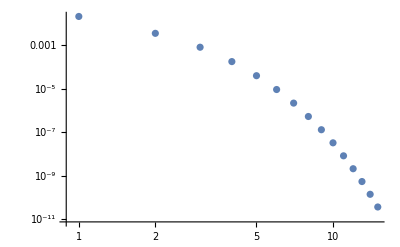

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2]Re[1/(2f)Sin[θ]h[9][r] YV1[l,m,θ,ϕ]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,15}]//ListLogLogPlot
```

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2]Re[h[9][r]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,50}]
```

{{0,0},{1,0.11196514735890058806834403427},{2,0.035668815437369630001306806024},{3,0.012409614096517425236984492134},{4,0.0036945462593946824462988419108},{5,0.0010620537243309881416160071172},{6,0.00030179891283167431212337478011},{7,0.000085400568497126194396227287584},{8,0.000024132025207696764466648148989},{9,6.8176300979050734659441114177×10^-6},{10,1.92668×10^-6},{11,5.44782×10^-7},{12,1.54139×10^-7},{13,4.36406×10^-8},{14,1.23637×10^-8},{15,3.50493×10^-9},{16,9.94178×10^-10},{17,2.82155×10^-10},{18,8.01188×10^-11},{19,2.27609×10^-11},{20,6.46899×10^-12},{21,1.83935×10^-12},{22,5.23189×10^-13},{23,1.48871×10^-13},{24,4.23749×10^-14},{25,1.20654×10^-14},{26,3.43642×10^-15},{27,9.79016×10^-16},{28,2.78988×10^-16},{29,7.95224×10^-17},{30,2.26726×10^-17},{31,6.46577×10^-18},{32,1.84416×10^-18},{33,5.26262×10^-19},{34,1.49895×10^-19},{35,4.25912×10^-20},{36,1.23116×10^-20},{37,3.41081×10^-21},{38,7.82799×10^-22},{39,7.26287×10^-23},{40,1.33044×10^-22},{41,1.93551×10^-22},{42,3.34325×10^-22},{43,1.93934×10^-22},{44,1.28635×10^-22},{45,2.1556×10^-22},{46,4.45272×10^-23},{47,2.85286×10^-22},{48,3.04728×10^-23},{49,1.90912×10^-22},{50,8.32108×10^-23}}

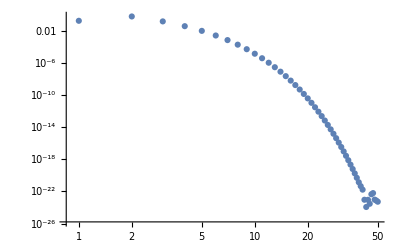

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2]Re[h[2,4][l,m]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,50}]//ListLogLogPlot
```

### Compute the difference between monopoles

```mathematica
monopoleReplace={
h[1][r]->h1l0-h1MonoOut[r0,r],
h[3][r]->h3l0-h3MonoOut[r0,r],
h[6][r]->h6l0-h6MonoOut[r0,r],
h[1]'[r]->D[h1l0-h1MonoOut[r0,r],r],
h[3]'[r]->D[h3l0-h3MonoOut[r0,r],r],
h[6]'[r]->D[h6l0-h6MonoOut[r0,r],r]
};
```

```mathematica
δhuu=Simplify[h[1,1][0,0] ut^2+2h[1,4][0,0]ut uϕ+h[4,4][0,0] uϕ^2/.monopoleReplace/.{r->r0,θ->π/2}];
δdrhuu=Simplify[D[h[1,1][0,0] ut^2+2h[1,4][0,0]ut uϕ+h[4,4][0,0] uϕ^2,r]/.monopoleReplace/.{r->r0,θ->π/2}];
```

### Regularization parameters h_ab

```mathematica
K=EllipticK[M/(r0-2M)];
Λ1=(l(l+1))/((2l-1)(2l+3));
Λ2=((l-1)l(l+1)(l+2))/((2l-3)(2l-1)(2l+3)(2l+5));
hP[1,1]=(4(r0-M)K)/(π r0^2)Sqrt[(r0-2M)/(r0-3M)];
hP[1,2]=0;
hP[1,3]=0;
hP[1,4]=-(32 M^(1/2)K)/(π r0^(1/2))Sqrt[(r0-2M)/(r0-3M)]Λ1;
hP[2,2]=(4K)/π(r0-3M)^(1/2)/(r0-2M)^(3/2);
hP[2,3]=0;
hP[2,4]=0;
hP[3,3]=(4r0 K)/π Sqrt[(r0-2M)/(r0-3M)]-(64M r0 K)/(π(r0-2M)^(1/2)(r0-3M)^(1/2))Λ2;
hP[3,4]=0;
hP[4,4]=(4r0 K)/π Sqrt[(r0-2M)/(r0-3M)]+(64M r0 K)/(π(r0-2M)^(1/2)(r0-3M)^(1/2))Λ2;
```

```mathematica
hR[a_,b_][l_]:=h[a,b][l]-hP[a,b]
```

```mathematica
Clear[hRlData]
hRlData[a_,b_]:=hRlData[a,b]=Table[{l,hR[a,b][l]},{l,0,lmax}];
```

```mathematica
Table[hRlData[a,b],{a,{1,4}},{b,{1,4}}];
```

### Regularization parameters h_(ab,r)

```mathematica
ℰ=EllipticE[M/(r0-2M)];
```

```mathematica
drhP[-1][1,1]=-(r0-M)/(r0^(5/2)(r0-3M)^(1/2));
drhP[0][1,1]=(2(r0-M)((r0-2M)ℰ-2(r0-4M)K))/(π r0^3(r0-3M)^(1/2)(r0-2M)^(1/2));
drhP[-1][1,2]=0;
drhP[0][1,2]=0;
drhP[-1][1,3]=0;
drhP[0][1,3]=0;
drhP[-1][1,4]=If[l≥1,(2 M^(1/2))/(r0(r0-3M)^(1/2)),0];
drhP[0][1,4]=-(16 M^(1/2)((r0-2 M) EllipticE[-M/(2 M-r0)]+2 M EllipticK[-M/(2 M-r0)]))/(π r0^(3/2)(r0-3M)^(1/2)(r0-2M)^(1/2))Λ1;

drhP[-1][2,2]=(-(r0-3 M)^(1/2))/(r0^(1/2) (r0-2 M)^2);
drhP[0][2,2]=(2 (r0-3M)^(1/2) ((r0-2 M)ℰ-2 r0 K))/(π r0 (r0-2 M)^(5/2));
drhP[-1][2,3]=0;
drhP[0][2,3]=0;
drhP[-1][2,4]=0;
drhP[0][2,4]=0;

drhP[-1][3,3]=-Sqrt[r0/(r0-3M)]+If[l≥2,(M r0^(1/2))/((r0-2M)(r0-3M)^(1/2)),0];
drhP[0][3,3]=2( ℰ+2K)/π Sqrt[(r0-2M)/(r0-3M)]-(32 M (ℰ+2K))/(π(r0-3M)^(1/2)(r0-2M)^(1/2))Λ2;
drhP[-1][3,4]=0;
drhP[0][3,4]=0;

drhP[-1][4,4]=- √(r0/(-3 M+r0))+If[l≥2,M/(√(1-(3 M)/r0) (2 M-r0)),0];
drhP[0][4,4]=(2  (EllipticE[-M/(2 M-r0)]+2 K))/π √((r0-2 M)/(r0-3 M))+Λ2(32M(ℰ+2 K))/(π (r0-3M)^(1/2)(r0-2M)^(1/2));
```

```mathematica
drhR[a_,b_][l_]:=drh[a,b][l]-drhP[-1][a,b](2l+1)-drhP[0][a,b]
```

```mathematica
Clear[drhRlData]
drhRlData[a_,b_]:=drhRlData[a,b]=Table[{l,drhR[a,b][l]},{l,0,lmax}];
```

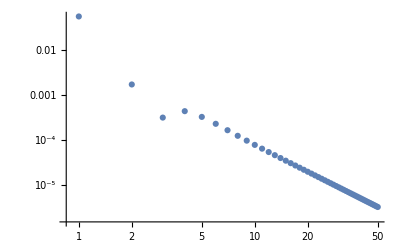

```mathematica
Show[
ListLogLogPlot[Abs[drhRlData[1,1]]]
]
```

### Regularization parameters h_(ab,ϕ)

```mathematica
dϕhP[-1][a_,b_]:=0;
dϕhP[0][1,1]=0;
dϕhP[0][1,2]=-(32((r0-2M)ℰ-(r0-3M)K))/(π M^(1/2)r0^(3/2))Sqrt[(r0-2M)/(r0-3M)]Λ1;
dϕhP[0][1,3]=0;
dϕhP[0][1,4]=0;
dϕhP[0][2,2]=0;
dϕhP[0][2,3]=0;
dϕhP[0][2,4]=(16((r0-2M) ℰ -(r0-3M)K))/(π(r0-2M)^(1/2)(r0-3M)^(1/2))(Λ1+4Λ2);
dϕhP[0][3,3]=0;
dϕhP[0][3,4]=0;
dϕhP[0][4,4]=0;
```

```mathematica
dϕhR[a_,b_][l_]:=dϕh[a,b][l]-dϕhP[-1][a,b](2l+1)-dϕhP[0][a,b]
```

```mathematica
Clear[dϕhRlData]
dϕhRlData[a_,b_]:=dϕhRlData[a,b]=Table[{l,dϕhR[a,b][l]},{l,0,lmax}];
```

### Regularization parameters h_(ab,t)

```mathematica
dthP[-1][a_,b_]:=0;
dthP[0][a_,b_]:=-Ωϕ dϕhP[0][a,b];
```

```mathematica
dthR[a_,b_][l_]:=dth[a,b][l]-dthP[-1][a,b](2l+1)-dthP[0][a,b]
```

```mathematica
Clear[dthRlData]
dthRlData[a_,b_]:=dthRlData[a,b]=Table[{l,dthR[a,b][l]},{l,0,lmax}];
```

### h_(ab,θ) has no regularization parameters

```mathematica
dθhP[-1][a_,b_]:=0;
dθhP[0][a_,b_]:=0;
```

```mathematica
dθhR[a_,b_][l_]:=dθh[a,b][l]-dθhP[-1][a,b](2l+1)-dθhP[0][a,b]
```

```mathematica
Clear[dθhRlData]
dθhRlData[a_,b_]:=dθhRlData[a,b]=Table[{l,dθhR[a,b][l]},{l,0,lmax}];
```

```mathematica
hRlData[2,4]//Abs//ListLogLogPlot
```

-Graphics-

```mathematica
hRlData[2,4]//Total
```

{1275,0.977599}

### Regularize

```mathematica
DetPoly[n_]:=Product[(2l-2k+1)(2l+2k+1),{k,1,n}]^-1;
AccelReg[data_,Nmax_,nmax_]:=FindFit[data[[-nmax;;]],Sum[RP[j]DetPoly[j],{j,1,Nmax}],Flatten[{Table[RP[j],{j,1,Nmax}]}],l];
```

```mathematica
hRlData2[a_,b_]:=hRlData2[a,b]=Block[{accel,dtaccel,draccel,dθaccel,dϕaccel,Nmax=10,nmax=25},
accel=AccelReg[hRlData[a,b],Nmax,nmax];
dtaccel=AccelReg[dthRlData[a,b],Nmax,nmax];
draccel=AccelReg[drhRlData[a,b],Nmax,nmax];
dθaccel=AccelReg[dθhRlData[a,b],Nmax,nmax];
dϕaccel=AccelReg[dϕhRlData[a,b],Nmax,nmax];
Table[{
l,
hRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.accel,{j,1,Nmax-1}],
dthRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.dtaccel,{j,1,Nmax-1}],
drhRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.draccel,{j,1,Nmax-1}],
dθhRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.dθaccel,{j,1,Nmax-1}],
dϕhRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.dϕaccel,{j,1,Nmax-1}]
},{l,0,Length[hRlData[a,b]]-1}]
]
```

```mathematica
huu=Total[hRlData2[1,1][[All,2]]] ut^2+2 Total[hRlData2[1,4][[All,2]]] ut uϕ+Total[hRlData2[4,4][[All,2]]] uϕ^2
```

-0.565786

```mathematica
(*hRlData2[1,1][[All,2]]//Total
hRlData[1,1][[All,2]]//Total

hRlData2[1,1][[All,4]]//Total
drhRlData[1,1][[All,2]]//Total*)
```

```mathematica
α=1/Sqrt[r0(r0-3)];
ΔU=(1-3/r0)^(-1/2)((r0-2)/(r0-3)α+1/2(huu+δhuu))
```

-0.29093

```mathematica
1-ΔU/ΔUres[[Flatten[Position[ΔUres[[All,1]],r0]]]][[1,2]]
```

Part::partw: Part 1 of {} does not exist.

1+0.29093/({}⟦1,2⟧)

```mathematica
Interpolation[Import["~/BHPToolkit/CircularOrbitSelfForceData/Schwarzschild/Redshift_and_spin_invariants.dat"][[7;;,{1,2}]],InterpolationOrder->5][r0]
```

-0.291616

```mathematica
(*For radiative components, which don't require regularization, use hRlData. Otherwise hRlData2*)
h1ab={
{1,1,Total[hRlData2[1,1][[;;,2]]],Total[dthRlData[1,1][[;;,2]]],Total[hRlData2[1,1][[;;,4]]]  ,Total[dθhRlData[1,1][[;;,2]]],Total[dϕhRlData[1,1][[;;,2]]]},
{1,2,Total[hRlData[1,2][[;;,2]]]  ,Total[hRlData2[1,2][[;;,3]]]  ,Total[drhRlData[1,2][[;;,2]]],Total[dθhRlData[1,2][[;;,2]]],Total[hRlData2[1,2][[;;,6]]] },
{1,3,Total[hRlData[1,3][[;;,2]]]  ,Total[dthRlData[1,3][[;;,2]]]  ,Total[drhRlData[1,3][[;;,2]]],Total[dθhRlData[1,3][[;;,2]]],Total[dϕhRlData[1,3][[;;,2]]] },
{1,4,Total[hRlData2[1,4][[;;,2]]],Total[dthRlData[1,4][[;;,2]]],Total[hRlData2[1,4][[;;,4]]]  ,Total[dθhRlData[1,4][[;;,2]]],Total[dϕhRlData[1,4][[;;,2]]]},
{2,2,Total[hRlData2[2,2][[;;,2]]],Total[dthRlData[2,2][[;;,2]]],Total[hRlData2[2,2][[;;,4]]]  ,Total[dθhRlData[2,2][[;;,2]]],Total[dϕhRlData[2,2][[;;,2]]]},
{2,3,Total[hRlData2[2,3][[;;,2]]],Total[dthRlData[2,3][[;;,2]]],Total[drhRlData[2,3][[;;,2]]],Total[hRlData2[2,3][[;;,5]]],Total[dϕhRlData[2,3][[;;,2]]]},
{2,4,Total[hRlData[2,4][[;;,2]]]  ,Total[hRlData2[2,4][[;;,3]]]  ,Total[drhRlData[2,4][[;;,2]]],Total[dθhRlData[2,4][[;;,2]]],Total[hRlData2[2,4][[;;,6]]]},
{3,3,Total[hRlData2[3,3][[;;,2]]],Total[dthRlData[3,3][[;;,2]]],Total[hRlData2[3,3][[;;,4]]]  ,Total[dθhRlData[3,3][[;;,2]]],Total[dϕhRlData[3,3][[;;,2]]]},
{3,4,Total[hRlData2[3,4][[;;,2]]],Total[dthRlData[3,4][[;;,2]]],Total[drhRlData[3,4][[;;,2]]]  ,Total[dθhRlData[3,4][[;;,2]]],Total[dϕhRlData[3,4][[;;,2]]]},
{4,4,Total[hRlData2[4,4][[;;,2]]],Total[dthRlData[4,4][[;;,2]]],Total[hRlData2[4,4][[;;,4]]]  ,Total[dθhRlData[4,4][[;;,2]]],Total[dϕhRlData[4,4][[;;,2]]]}
}
```

{{1,1,-0.356603,0.0050867,0.0740877,0.,-0.0756954},{1,2,-0.0883308,-0.00856653,-0.0047851,0.,0.127479},{1,3,0.,0.,0.,0.511873,0.},{1,4,0.932581,-0.0538296,0.00259307,0.,0.801041},{2,2,-0.089085,-0.0256865,-0.0382956,0.,0.382242},{2,3,0.,0.,0.,-0.299924,0.},{2,4,0.977599,0.0285046,0.0648728,0.,-0.424178},{3,3,-6.14159,0.200569,1.0187,0.,-2.98467},{3,4,0.,0.,0.,-3.5086,0.},{4,4,-11.9506,0.757736,-0.217009,0.,-11.2759}}

```mathematica
(*SetDirectory["/Users/niels/Dropbox/Mathematica/2nd_order/h1_ab data/"];*)
SetDirectory["~/Code/SecondOrder/FirstOrderData/data/R_data/"];
data=Import["h1Rab.dat"];
pos=Position[data[[All,1]],N[r0]];
If[Length[pos]==0,
AppendTo[data,Flatten[{N[r0],h1ab[[All,3]],h1ab[[All,4]],h1ab[[All,5]],h1ab[[All,6]],h1ab[[All,7]]}]];,
If[Length[pos]==1,
data[[pos[[1]]]]=Flatten[{N[r0],h1ab[[All,3]],h1ab[[All,4]],h1ab[[All,5]],h1ab[[All,6]],h1ab[[All,7]]}];,
Print["Two data entries for r0=" <>ToString[r0]]
]
]
Export["h1Rab.dat",Sort[data]];
```

## Calculate the radial self-force

Check results for asymptotically flat monopole against Berndtson’s thesis

```mathematica
dhRlData2[a_,b_]:=Block[{accel,Nmax=10,nmax=25},
accel=AccelReg[drhRlData[a,b],Nmax,nmax];
Table[{l,drhRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.accel,{j,1,Nmax-1}]},{l,0,Length[drhRlData[a,b]]-1}]
]
```

```mathematica
drhuu=Total[dhRlData2[1,1][[All,2]]] ut^2+2 Total[dhRlData2[1,4][[All,2]]] ut uϕ+Total[dhRlData2[4,4][[All,2]]] uϕ^2
```

0.145708

```mathematica
{FrReg,FrIrreg}={1/2(1-(2M)/r0)drhuu,1/2(1-(2M)/r0)(drhuu+δdrhuu)}
```

{0.0487701,0.0243494}

```mathematica
Akcay={{6,2.4466495 10^-2},{8,1.8357830 10^-2},{10,1.3389470 10^-2}};
Berndtson={{6,4.9685669 10^-2},{8,2.7112763 10^-2},{10,1.7454613 10^-2}};
```

```mathematica
SetDirectory["~/Code/SecondOrder/FirstOrderData/data/R_data/"];
data=Import["Fr.dat"];
pos=Position[data[[All,1]],r0];
If[Length[pos]==0,
AppendTo[data,{N[r0],FrReg,FrIrreg}],
If[Length[pos]==1,
data[[pos[[1]]]]={N[r0],FrReg,FrIrreg},
Print["Two data entries for r0=" <>ToString[r0]]
]
]
Export["Fr.dat",Sort[data]]
```

{{5,0.077252,0.023974},{5.25,0.0681242,0.0249093},{5.5,0.0607852,0.0251424},{5.75,0.0547463,0.0249397},{6,0.0496857,0.0244665},{6.25,0.0453817,0.0238283},{6.3,0.0445969,0.0236873},{6.4,0.0430947,0.0233957},{6.5,0.0416762,0.0230935},{6.6,0.0403345,0.0227832},{6.7,0.0390636,0.0224669},{6.8,0.0378581,0.0221465},{6.9,0.0367133,0.0218234},{7,0.0356247,0.0214991},{7.1,0.0345883,0.0211745},{7.2,0.0336006,0.0208506},{7.3,0.0326583,0.0205282},{7.4,0.0317584,0.020208},{7.5,0.0308983,0.0198906},{7.6,0.0300753,0.0195763},{7.7,0.0292873,0.0192656},{7.8,0.0285322,0.0189588},{7.9,0.0278079,0.0186561},{8,0.0271128,0.0183578},{8.1,0.0264451,0.0180641},{8.2,0.0258034,0.017775},{8.3,0.0251861,0.0174907},{8.4,0.0245922,0.0172112},{8.5,0.0240202,0.0169366},{8.6,0.023469,0.0166669},{8.7,0.0229376,0.0164022},{8.8,0.0224251,0.0161423},{8.9,0.0219304,0.0158873},{9,0.0214527,0.0156371},{9.1,0.0209912,0.0153917},{9.2,0.0205451,0.0151511},{9.3,0.0201138,0.0149152},{9.4,0.0196965,0.0146839},{9.5,0.0192926,0.0144572},{9.6,0.0189015,0.014235},{9.7,0.0185227,0.0140172},{9.8,0.0181556,0.0138037},{9.9,0.0177997,0.0135945},{10,0.0174546,0.0133895},{10.1,0.0171198,0.0131886},{10.2,0.0167949,0.0129917},{10.3,0.0164794,0.0127987},{10.4,0.0161731,0.0126096},{10.5,0.0158755,0.0124243},{10.6,0.0155863,0.0122427},{10.7,0.0153052,0.0120647},{10.8,0.0150318,0.0118903},{10.9,0.0147659,0.0117193},{11,0.0145072,0.0115517},{11.1,0.0142555,0.0113875},{11.2,0.0140104,0.0112264},{11.3,0.0137718,0.0110686},{11.4,0.0135393,0.0109138},{11.5,0.0133129,0.010762},{11.6,0.0130922,0.0106132},{11.7,0.0128771,0.0104673},{11.8,0.0126674,0.0103242},{11.9,0.0124628,0.0101839},{12,0.0122634,0.0100462},{12.1,0.0120687,0.00991122},{12.2,0.0118788,0.00977877},{12.3,0.0116934,0.00964884},{12.4,0.0115124,0.00952135},{12.5,0.0113357,0.00939626},{12.6,0.011163,0.00927352},{12.7,0.0109944,0.00915306},{12.8,0.0108297,0.00903483},{12.9,0.0106686,0.00891879},{13.,0.0105112,0.00880489},{13.1,0.0103574,0.00869306},{13.2,0.0102069,0.00858328},{13.3,0.0100598,0.00847549},{13.4,0.00991585,0.00836964},{13.5,0.00977504,0.0082657},{13.6,0.00963725,0.00816362},{13.7,0.0095024,0.00806335},{13.8,0.00937041,0.00796486},{13.9,0.00924119,0.00786811},{14.,0.00911467,0.00777306},{14.1,0.00899076,0.00767967},{14.2,0.0088694,0.0075879},{14.3,0.00875052,0.00749773},{14.4,0.00863404,0.0074091},{14.5,0.00851991,0.007322},{14.6,0.00840805,0.00723638},{14.7,0.00829841,0.00715222},{14.8,0.00819093,0.00706948},{14.9,0.00808555,0.00698813},{15.,0.00798222,0.00690815},{15.1,0.00788088,0.00682949},{15.2,0.00778148,0.00675215},{15.3,0.00768397,0.00667608},{15.4,0.00758831,0.00660126},{15.5,0.00749444,0.00652766},{15.6,0.00740232,0.00645526},{15.7,0.0073119,0.00638403},{15.8,0.00722316,0.00631395},{15.9,0.00713603,0.006245},{16.,0.00705049,0.00617715},{16.1,0.00696649,0.00611037},{16.2,0.006884,0.00604465},{16.3,0.00680299,0.00597997},{16.4,0.0067234,0.0059163},{16.5,0.00664522,0.00585363},{16.6,0.00656841,0.00579192},{16.7,0.00649294,0.00573117},{16.8,0.00641877,0.00567136},{16.9,0.00634587,0.00561246},{17.,0.00627423,0.00555446},{17.1,0.0062038,0.00549734},{17.2,0.00613455,0.00544108},{17.3,0.00606648,0.00538567},{17.4,0.00599953,0.00533109},{17.5,0.0059337,0.00527732},{17.6,0.00586896,0.00522435},{17.7,0.00580528,0.00517216},{17.8,0.00574263,0.00512073},{17.9,0.00568101,0.00507006},{18.,0.00562037,0.00502013},{18.1,0.00556072,0.00497092},{18.2,0.00550201,0.00492242},{18.3,0.00544423,0.00487462},{18.4,0.00538737,0.00482751},{18.5,0.0053314,0.00478106},{18.6,0.0052763,0.00473527},{18.7,0.00522206,0.00469013},{18.8,0.00516866,0.00464563},{18.9,0.00511607,0.00460174},{19.,0.00506429,0.00455847},{19.1,0.0050133,0.0045158},{19.2,0.00496308,0.00447372},{19.3,0.00491362,0.00443221},{19.4,0.00486489,0.00439128},{19.5,0.0048169,0.0043509},{19.6,0.00476961,0.00431108},{19.7,0.00472302,0.00427179},{19.8,0.00467711,0.00423303},{19.9,0.00463187,0.00419479},{20.,0.0045873,0.00415706},{20.1,0.00454336,0.00411983},{20.2,0.00450006,0.00408309},{20.3,0.00445737,0.00404684},{20.4,0.0044153,0.00401106},{20.5,0.00437382,0.00397576},{20.6,0.00433292,0.00394091},{20.7,0.0042926,0.00390651},{20.8,0.00425284,0.00387256},{20.9,0.00421364,0.00383905},{21.,0.00417498,0.00380596},{21.1,0.00413685,0.0037733},{21.2,0.00409924,0.00374105},{21.3,0.00406214,0.00370921},{21.4,0.00402555,0.00367777},{21.5,0.00398946,0.00364673},{21.6,0.00395385,0.00361607},{21.7,0.00391871,0.0035858},{21.8,0.00388405,0.0035559},{21.9,0.00384984,0.00352637},{22.,0.00381609,0.0034972},{22.1,0.00378278,0.0034684},{22.2,0.00374991,0.00343994},{22.3,0.00371747,0.00341183},{22.4,0.00368544,0.00338406},{22.5,0.00365383,0.00335663},{22.6,0.00362263,0.00332952},{22.7,0.00359183,0.00330274},{22.8,0.00356142,0.00327628},{22.9,0.00353139,0.00325013},{23.,0.00350175,0.0032243},{23.1,0.00347248,0.00319877},{23.2,0.00344358,0.00317353},{23.3,0.00341503,0.0031486},{23.4,0.00338684,0.00312395},{23.5,0.003359,0.00309959},{23.6,0.00333151,0.00307551},{23.7,0.00330435,0.00305171},{23.8,0.00327752,0.00302819},{23.9,0.00325102,0.00300493},{24.,0.00322484,0.00298194},{24.1,0.00319898,0.00295921},{24.2,0.00317343,0.00293674},{24.3,0.00314818,0.00291452},{24.4,0.00312324,0.00289255},{24.5,0.00309859,0.00287082},{24.6,0.00307424,0.00284934},{24.7,0.00305017,0.0028281},{24.8,0.00302638,0.00280709},{24.9,0.00300287,0.00278632},{25.,0.00297964,0.00276577},{25.1,0.00295667,0.00274545},{25.2,0.00293397,0.00272535},{25.3,0.00291153,0.00270547},{25.4,0.00288935,0.0026858},{25.5,0.00286742,0.00266635},{25.6,0.00284574,0.0026471},{25.7,0.00282431,0.00262807},{25.8,0.00280312,0.00260923},{25.9,0.00278217,0.0025906},{26.,0.00276145,0.00257217},{26.1,0.00274096,0.00255393},{26.2,0.0027207,0.00253588},{26.3,0.00270067,0.00251802},{26.4,0.00268085,0.00250035},{26.5,0.00266126,0.00248286},{26.6,0.00264188,0.00246556},{26.7,0.00262271,0.00244843},{26.8,0.00260375,0.00243149},{26.9,0.00258499,0.00241471},{27.,0.00256644,0.00239811},{27.1,0.00254809,0.00238168},{27.2,0.00252993,0.00236542},{27.3,0.00251197,0.00234932},{27.4,0.0024942,0.00233338},{27.5,0.00247661,0.00231761},{27.6,0.00245922,0.00230199},{27.7,0.002442,0.00228653},{27.8,0.00242497,0.00227123},{27.9,0.00240811,0.00225607},{28.,0.00239143,0.00224107},{28.1,0.00237493,0.00222622},{28.2,0.00235859,0.00221151},{28.3,0.00234242,0.00219695},{28.4,0.00232642,0.00218253},{28.5,0.00231058,0.00216825},{28.6,0.00229491,0.00215411},{28.7,0.00227939,0.00214011},{28.8,0.00226403,0.00212625},{28.9,0.00224883,0.00211251},{29.,0.00223377,0.00209891},{29.1,0.00221887,0.00208544},{29.2,0.00220412,0.0020721},{29.3,0.00218952,0.00205889},{29.4,0.00217506,0.0020458},{29.5,0.00216074,0.00203283},{29.6,0.00214657,0.00201999},{29.7,0.00213253,0.00200727},{29.8,0.00211863,0.00199467},{29.9,0.00210487,0.00198218},{30.,0.00209124,0.00196982},{30.1,0.00207774,0.00195756},{30.2,0.00206438,0.00194543},{30.3,0.00205114,0.0019334},{30.4,0.00203803,0.00192148},{30.5,0.00202505,0.00190968},{30.6,0.00201219,0.00189798},{30.7,0.00199945,0.00188638},{30.8,0.00198683,0.0018749},{30.9,0.00197433,0.00186352},{40,0.00119293,0.00114288},{50,0.000770228,0.000744949},{60,0.000538113,0.000523614},{70,0.000397083,0.00038801},{6.05,0.0487701,0.0243494}}

Fr.dat

## Checks

The weird behavior below seems to only be in r_0=8M for i=9.

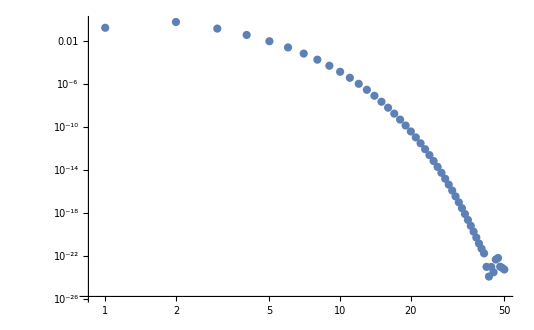

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2]Re[h[2,4][l,m]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,50}]//ListLogLogPlot
```

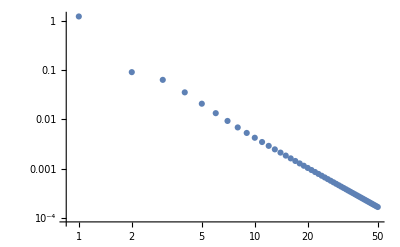

```mathematica
ListLogLogPlot[hRlData[1,4]//Re//Abs]
```

```mathematica
Quit[]
```